```mathematica
ParametricPlot3D[{Sin[t],(Sin[t])^2,0},{t,0,2Pi}]
```

-Graphics3D-

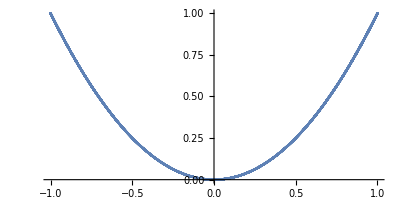

```mathematica
A1=ParametricPlot[{Sin[t],(Sin[t])^2},{t,-8Pi,8Pi}]
```

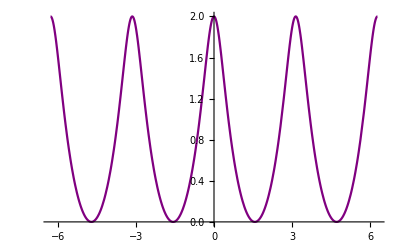

```mathematica
A2=Plot[(2*((Cos[t])^2))/(Sqrt[(1+(4*(Sin[t]^2)))]),{t,-2Pi,2Pi},PlotStyle->Purple]
```

```mathematica
(*La recta asíntota de la curvatura (en púrpura), parece permanecer entre 0 y 2.*)
```

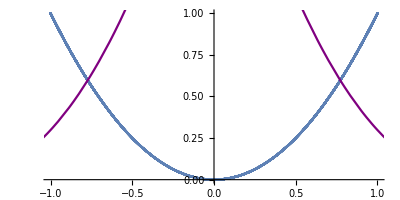

```mathematica
Show[A1,A2]
```

```mathematica
f[x_,y_]:=(2*((Cos[t])^2))/(Sqrt[(1+(4*(Sin[t]^2)))])
pc={x,y,f[x,y]}/.Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y},Reals]
a=ContourPlot3D[z==f[x,y],{x,-3,3},{y,-3,3},{z,-2,2},PlotPoints->40,Mesh->False,Boxed->False,Axes->False];
b=Graphics3D[{PointSize[0.04],Black,Point[pc]}];
Show[b,a,BoxRatios->{3,3,2}]
```

{{x,y,(2 Cos[t]^2)/(√(1+4 Sin[t]^2))}}

Show::gcomb: Could not combine the graphics objects in Show[,ContourPlot3D[z==f[x,y],{x,-3,3},{y,-3,3},{z,-2,2},PlotPoints→40,Mesh→False,Boxed→False,Axes→False],BoxRatios→{3,3,2}].

Show[-Graphics3D-,ContourPlot3D[z==f[x,y],{x,-3,3},{y,-3,3},{z,-2,2},PlotPoints→40,Mesh→False,Boxed→False,Axes→False],BoxRatios→{3,3,2}]